# Spike Sorting Tests Loosely Based on Quiroga

```mathematica
<<NounouW`
```

HokahokaW`
Git HEAD hash loaded on Mon 15 Jun 2015 11:18:14 is 4b7a2925e5f751bf058f0f604c6362452e9e2c30.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

<<Set JLink` java stack size to 6144Mb>>

NounouW`
Git HEAD hash loaded on Tue 15 Sep 2015 12:44:29 is 36142530092fa937de2a5103a71fe8734f3061ee.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 3cc31723ae141d3f2622c7f26ab9e5a96b19674c
  + current branch is: master
  + remote names are: https://ktakagaki@github.com/ktakagaki/nounou.git

```mathematica
NotebookDirectory[]
```

C:\prog\nounou\src\test\mathematica\nounou\analysis\spikes\

```mathematica
nnDataDirectory=FileNameJoin[
{Nest[ParentDirectory,NotebookDirectory[],7],
"nounou-resources","resources","nounou","Neuralynx","SPP010","2013-12-02_17-07-31"}]
```

C:\prog\nounou-resources\resources\nounou\Neuralynx\SPP010\2013-12-02_17-07-31

```mathematica
nnDataFiles=FileNames[FileNameJoin[{nnDataDirectory,"*.ncs"}]]
```

{C:\prog\nounou-resources\resources\nounou\Neuralynx\SPP010\2013-12-02_17-07-31\Tet4a.ncs,C:\prog\nounou-resources\resources\nounou\Neuralynx\SPP010\2013-12-02_17-07-31\Tet4b.ncs,C:\prog\nounou-resources\resources\nounou\Neuralynx\SPP010\2013-12-02_17-07-31\Tet4c.ncs,C:\prog\nounou-resources\resources\nounou\Neuralynx\SPP010\2013-12-02_17-07-31\Tet4d.ncs}

```mathematica
nnData=NN`load[nnDataFiles][[1]]
```

{«JavaObject[nounou.elements.data.NNDataChannelArray]»}

```mathematica
nnDataFiltered=JavaNew["nounou.elements.data.filters.NNDataFilterMedianSubtract",nnData]
```

Java::excptn: A Java exception occurred: "java.lang.NullPointerException\n\tat nounou.elements.data.filters.NNDataFilterBuffer.flushBuffer(NNDataFilterBuffer.scala:56)\n\tat nounou.elements.data.filters.NNDataFilterBuffer.changedData(NNDataFilterBuffer.scala:43)\n\tat nounou.elements.data.filters.NNDataFilter.setParent(NNDataFilter.scala:24)\n\tat nounou.elements.data.filters.NNDataFilter.<init>(NNDataFilter.scala:16)\n\tat nounou.elements.data.filters.NNDataFilterBuffer.<init>(NNDataFilterBuffer.scala:17)\n\tat nounou.elements.data.filters.NNDataFilterMedianSubtract.<init>(NNDataFilterMedianSubtract.scala:19)\n\tat sun.reflect.NativeConstructorAccessorImpl.newInstance0(Native Method)\n\tat sun.reflect.NativeConstructorAccessorImpl.newInstance(NativeConstructorAccessorImpl.java:62)\n\tat sun.reflect.DelegatingConstructorAccessorImpl.newInstance(DelegatingConstructorAccessorImpl.java:45)\n\tat java.lang.reflect.Constructor.newInstance(Constructor.java:422)".

JavaNew::fail: Error calling constructor for class "nounou.elements.data.filters.NNDataFilterMedianSubtract".

$Failed

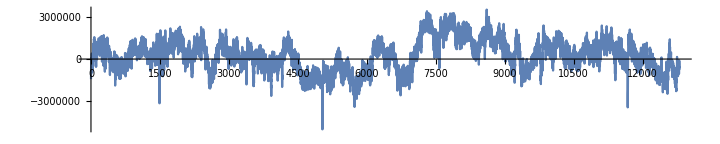

```mathematica
ListLinePlot[nnData@readTrace[0, NN`SampleRange[76800,80800,1,0]],
AspectRatio->1/5,ImageSize->72*10]
```